```mathematica
i
```

i

```mathematica
λ0=1;ηl=2;x0=1;ηx=2; (* This one is the multi-model one *)
(*λ0=1;ηl=1.01;x0=1;ηx=1; (*This one is where our profile on lambda breaks down *)*)
(*λ0=1;ηl=3;x0=1;ηx=0.5;*)
```

```mathematica
λ*Abs[x]+(λ-λ0)^2/(2*ηl)+(x-x0)^2/(2*ηx)/.{λ->1,x->0}
```

1/4

```mathematica
Max[0,x0-ηx*((λ0-ηl*Abs[x0]) / (1-ηl*ηx))]*Sign[x0]
```

1/3

```mathematica
(λ0-ηl*Abs[x0]) (* The numerator of the solution *)
```

-1

```mathematica
Abs[x0]/ηx (* The transition point*)
```

1/2

```mathematica
Minimize[{λ*Abs[x]+(λ-λ0)^2/(2*ηl)+(x-x0)^2/(2*ηx),λ>0},{x,λ}]
```

{1/4,{x→0,λ→1}}

```mathematica
(* Optimum of lower interval *)
```

```mathematica
(λ0-ηl*Abs[x0]) / (1-ηl*ηx)
```

1/3

```mathematica
Abs[x0]/ηx
λ0/ηl
```

1/2

1/2

```mathematica
(λ-λ0)^2/(2*ηl)+λ*Max[0,Abs[x0]-ηx*λ]+(Max[0,Abs[x0]-ηx*λ]^2-2*Abs[x0]*Max[0,Abs[x0]-ηx*λ]+x0^2)/(2*ηx)
```

1/4 (-1+λ)^2+λ Max[0,1-2 λ]+1/4 (1-2 Max[0,1-2 λ]+Max[0,1-2 λ]^2)

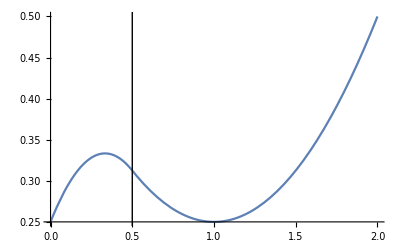

```mathematica
Plot[(λ-λ0)^2/(2*ηl)+λ*Max[0,Abs[x0]-ηx*λ]+(Max[0,Abs[x0]-ηx*λ]^2-2*Abs[x0]*Max[0,Abs[x0]-ηx*λ]+x0^2)/(2*ηx),{λ,0,2},Epilog->{(*add vertical lines*)InfiniteLine[{Abs[x0]/ηx,0},{0,1}]}](*Can you add dotted lines showing how the piecewise quadratics would continue?*)
```

```mathematica
Plot[(λ-λ0)^2/(2*ηl)+λ*Max[0,Abs[x0]-ηx*λ]+(Max[0,Abs[x0]-ηx*λ]^2-2*Abs[x0]*Max[0,Abs[x0]-ηx*λ]+x0^2)/(2*ηx),{λ,0,2},Epilog->{(*add vertical lines*)InfiniteLine[{Abs[x0]/ηx,0},{0,1}]}]
```

-Graphics-

```mathematica
Hold[Piecewise[{{0.5*(1/ηl-ηx)*λ^2+(Abs[x0]-λ0/ηl)*λ+λ0^2/(2*ηl),λ<Abs[x0]/ηx},{1/(2*ηl)*λ^2-λ0/ηl*λ+λ0^2/(2*ηl)+x0^2/(2*ηx),λ>Abs[x0]/ηx}}]]
```

Hold[Piecewise[{{0.5 (1/ηl-ηx) λ^2+(Abs[x0]-λ0/ηl) λ+λ0^2/(2 ηl), λ<Abs[x0]/ηx}, {λ^2/(2 ηl)-(λ0 λ)/ηl+λ0^2/(2 ηl)+x0^2/(2 ηx), λ>Abs[x0]/ηx}}]]

```mathematica
Plot[Piecewise[{{0.5*(1/ηl-ηx)*λ^2+(Abs[x0]-λ0/ηl)*λ+λ0^2/(2*ηl),λ<Abs[x0]/ηx},{1/(2*ηl)*λ^2-λ0/ηl*λ+λ0^2/(2*ηl)+x0^2/(2*ηx),λ>Abs[x0]/ηx}}],{λ,0,2},Epilog->{(*add vertical lines*)InfiniteLine[{Abs[x0]/ηx,0},{0,1}]}] (*The proximal cost marginalized over x expressed as a piecewise quadratic *)
```

-Graphics-

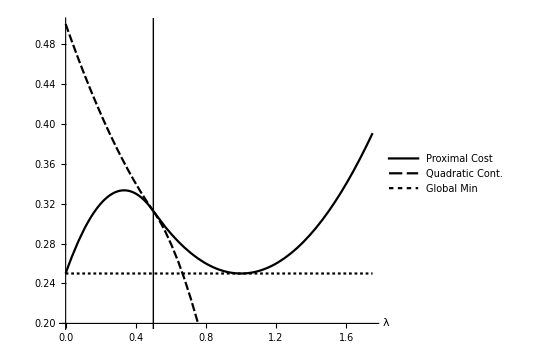

```mathematica
p1=Plot[{Piecewise[{{0.5*(1/ηl-ηx)*λ^2+(Abs[x0]-λ0/ηl)*λ+λ0^2/(2*ηl),λ<Abs[x0]/ηx},{1/(2*ηl)*λ^2-λ0/ηl*λ+λ0^2/(2*ηl)+x0^2/(2*ηx),λ>Abs[x0]/ηx}}],Piecewise[{{0.5*(1/ηl-ηx)*λ^2+(Abs[x0]-λ0/ηl)*λ+λ0^2/(2*ηl),λ>Abs[x0]/ηx},{1/(2*ηl)*λ^2-λ0/ηl*λ+λ0^2/(2*ηl)+x0^2/(2*ηx),λ<Abs[x0]/ηx}}],0.25},{λ,0,1.75},Epilog->{(*add vertical lines*)InfiniteLine[{Abs[x0]/ηx,0},{0,1}]},PlotRange->{0.2,0.5},PlotTheme->"Monochrome",PlotLegends->Placed[{Style["Proximal Cost",FontSize->20],Style["Quadratic Cont.",FontSize->20],Style["Global Min",FontSize->20]},{0.7,0.75}],AxesLabel->{Style["λ",Bold,18],,""},TicksStyle->Directive[Black, Opacity[0],Bold, FontOpacity->1],FrameTicks->None,AspectRatio->0.9]
```

```mathematica
Export["prox_cost.pdf",p1]
```

prox_cost.pdf

```mathematica
p2=Plot3D[{λ*Abs[x],0},{λ,0,2},{x,-2.5,2.5},AxesLabel->{Style[λ,Bold,18],Style[β,Bold,18]},PlotPoints->60,Boxed->False,ViewPoint->{-2, -2, 1}]
```

```mathematica
-Graphics3D-
Export["biconv_pen.pdf",p2]
```

-Graphics3D-

biconv_pen.pdf

-Graphics3D-

```mathematica
Export["biconv_pen.pdf",p2]
```

biconv_pen.pdf

```mathematica
p3=Plot3D[{λ*Abs[x]+(λ-λ0)^2/(2*ηl)+(x-x0)^2/(2*ηx),0,0,0.325},{λ,0,2},{x,-1,2.5},AxesLabel->{Style[β,Bold,18],Style[λ,Bold,18]},PlotRange->{0.25,1},PlotPoints->60,ViewPoint->{-3,0.5,1.5},TicksStyle->Directive[Black, Opacity[0],Bold, FontOpacity->1],BoxRatios->{0.8,0.6,0.25},Lighting->{{"Ambient", White}},PlotStyle->{"",Opacity[0.6]}]
```

-Graphics3D-

```mathematica
Export["nonconv_cost.pdf",p3]
```

nonconv_cost.pdf

```mathematica
bb=0.1;pp = Plot3D[Piecewise[{{λ0,λ0>a},{Max[0,λ0-a*bb]/(1-bb),λ0<a}}],{λ0,0,2},{a,0,2},ColorFunction->"DarkRainbow",AxesLabel->{Style[λ0,FontSize->18],Style[HoldForm[β0/sβ],FontSize->18],Style[λ,FontSize->18]}]
```